## On Spectral Decomposition of de Sitter 4pt Function

```mathematica
rhoFree[nu_]:=Gamma[d/2](Gamma[I nuPhi])^4 Gamma[d/2+I nu]Gamma[d/2-I nu]Gamma[(d-4 I nuPhi + 2 I nu)/4]Gamma[(d-4 I nuPhi - 2 I nu)/4]/(64 Pi^(3 d/2 + 3) Gamma[I nu] Gamma[-I nu]Gamma[(d+4 I nuPhi + 2 I nu)/4]Gamma[(d+4 I nuPhi - 2 I nu)/4]);


A[nu_]:=(Gamma[I nuPhi])^4/(2^10 Pi^(2 d+ 5)) Sin[Pi/2(d/2-I nu - 2I nuPhi)]^2(Gamma[(d-4 I nuPhi + 2 I nu)/4])^2(Gamma[(d-4 I nuPhi - 2 I nu)/4])^2 (Gamma[(d+2 I nu)/4]Gamma[(d-2I nu)/4])^2 nu/(Pi I);

AT[nu_]:=(Gamma[I nuPhi])^4 Pi^(d/2) Gamma[I nu]/(2^10 Pi^(2 d+ 5)) Sin[Pi/2(d/2-I nu - 2I nuPhi)]^2(Gamma[(d-4 I nuPhi + 2 I nu)/4])^2(Gamma[(d-4 I nuPhi - 2 I nu)/4])^2 (Gamma[(d-2 I nu)/4])^4 nu/(Pi I Gamma[d/2-I nu]);


Cblock[nu_]:=Pi^(d/2) Gamma[-I nu]Gamma[d/4+ I nu/2]^2 /(Gamma[d/2+I nu] Gamma[d/4-I nu/2]^2);
```

```mathematica
rho[nu_]:=rhoFree[nu]+g^2/2(A[nu]+A[-nu])/(nu^2-nuSig^2);
```

### Comments On Analytic form of Spectral Function

The integrand of the spectral representation is  f^(4pt)(ν) C_-v * (Conformal Block for scalar exchange  Δ= d/2 - i ν ). Blocks are known analytically.

f^(4pt)(ν) = g^2 f^(2pt)(ν) A(ν) , and  f^(2pt)(ν) = 1/(ν^2-ν_σ^2 -  g^2 B(ν)/2)

B(ν) has single poles in upper half plane at double trace positions. 
νPP(n) = 2 ν_ϕ + i d/2 + 2 i n , νPN(n) = i d/2 + 2 i n , νNN(n) = -2 ν_ϕ + i d/2 + 2 i n ; n ϵ ℤ^+∪ {0}
write code that produces the residues of B(ν) at these poles

A(ν) C_-ν has double poles at upper half plane at positions νPP(n) = 2 ν_ϕ + i d/2 + 2 i n coming from Gamma functions of A(ν). Other poles are for Im(ν) <= -d/2, so doesn’t bother us.

The full  f^(4pt)(ν) has single poles at shifted upper half plane double trace positions: νPP(n)+δνPP(n), νPN(n)+δνPN(n), νNN(n)+δνNN(n).
Shifts are known and Residues at Shifts are also known.

### Residues of B(ν), A(ν), f^(4pt)(ν)C_-ν

```mathematica
a[delta1_,delta2_,n_]:=Pochhammer[d/2,n]Pochhammer[-d+n+delta1+delta2+1,n]Pochhammer[2n+delta1+delta2,1-d/2]/(2 n! Pi^(d/2) Pochhammer[n+delta1,1-d/2]Pochhammer[n+delta2,1-d/2]Pochhammer[-d/2+n+delta1+delta2,n]);
```

```mathematica
resBAdS[nu1_,nu2_]:=Table[1/2 a[d/2+I nu1, d/2 + I nu2,n]/(2 I n + I d/2 - nu1 -nu2),{n,0,nmax}];
```

```mathematica
resBdS[k_,n_]:=I/(4 Pi^2) (nuPhi)^2(Gamma[I nuPhi]Gamma[-I nuPhi])^2 Which[k==-2, (1-Exp[I Pi (d+ 4 I nuPhi)])resBAdS[nuPhi,nuPhi][[n+1]],k==2,(1-Exp[I Pi (d- 4 I nuPhi)])resBAdS[-nuPhi,-nuPhi][[n+1]] ,k==0, -2(1-Exp[I Pi (d)])resBAdS[-nuPhi,nuPhi][[n+1]]];
```

```mathematica
polesPP[n_]:=2 nuPhi + I d/2 + 2 I n;
polesNN[n_]:=-2 nuPhi + I d/2 + 2 I n;
polesPN[n_]:=I d/2 + 2 I n;
```

We need to evaluate  A_-2 at νPP(n) and  A_0 at νPN(n) and νNN(n)

```mathematica
minus2APP[n_]:=((-1)^n/n!)^2(2/I)^2(((A[nu]Cblock[-nu]/(Gamma[(d-4 I nuPhi + 2 I nu)/4])^2) //Simplify)/.nu->polesPP[n]);
zeroANN[n_]:=(AT[nu])/.nu->polesNN[n];
zeroAPN[n_]:=(AT[nu])/.nu->polesPN[n];
```

```mathematica
ShiftPP[n_]:= g^2 resBdS[2,n]/(2(polesPP[n]^2-nuSig^2));
ShiftPN[n_]:= g^2 resBdS[0,n]/(2(polesPN[n]^2-nuSig^2));
ShiftNN[n_]:= g^2 resBdS[-2,n]/(2(polesNN[n]^2-nuSig^2));
```

```mathematica
resf4ptCPP[n_]:= 2minus2APP[n]/resBdS[2,n];
resf4ptCPN[n_]:= 2 zeroAPN[n]/resBdS[0,n] (ShiftPN[n])^2;
resf4ptCNN[n_]:= 2 zeroANN[n]/resBdS[-2,n] (ShiftNN[n])^2;
```

## Scalar Conformal Blocks for any d

#### Closed Form Expression for d=4

```mathematica
k[beta_,x_]:=x^(beta/2)Hypergeometric2F1[beta/2,beta/2,beta,x];
g4[delta_,z_,zbar_]:=(z zbar)/(z-zbar) (k[delta,z]k[delta-2,zbar]-k[delta,zbar]k[delta-2,z]);
```

#### Series Approximation for any d

```mathematica
gblock[d_,Δ_,z_,zbar_]:=(z zbar)^(Δ/2)Sum[Sum[((Pochhammer[Δ/2,m1]Pochhammer[Δ/2,m1+m2])^2 u^m1(1-v)^m2)/(m1! m2! Pochhammer[Δ+1-d/2,m1]Pochhammer[Δ,2m1+m2])/.{u->z zbar,v->(1-z)(1-zbar)},{m1,0,m1max}],{m2,0,m2max}]
```

#### Some Checks

```mathematica
m1max=15;
m2max=65;
```

```mathematica
gblock[4,3,1/1.5-0.01,1/1.5+0.01]
```

1.41605

```mathematica
g4[3,1/1.5-0.01,1/1.5+0.01]
```

1.41612

## Conformal Block expansion up to (n+1)th term

```mathematica
CblockExpansion1[z_,zbar_,n_]:=2 Pi I Sum[(resf4ptCPP[l] g4[polesPP[l],z,zbar]+resf4ptCPN[l] g4[polesPN[l],z,zbar]+resf4ptCNN[l] g4[polesNN[l],z,zbar]),{l,0,n}];
CblockExpansion2[n_]:=2 Pi I Sum[(resf4ptCPP[l] g4[polesPP[l],2+
1/1000,2-1/1000]+resf4ptCPN[l] g4[polesPN[l],1/2+1/1000,2-1/1000]+resf4ptCNN[l] g4[polesNN[l],2+1/1000,2-1/1000]),{l,0,n}];
CblockExpansion3[z_,zbar_,n_]:=2 Pi I Sum[(resf4ptCPN[l] g4[polesPN[l],z,zbar]+resf4ptCNN[l] g4[polesNN[l],z,zbar]),{l,0,n}];
```

```mathematica
nmax=50;
```

```mathematica
rules={d->4+1/100000,nuPhi->-I/8,nuSig->1/8,g->1/100};
```

```mathematica
CblockExpansion[3]/.rules
```

0.00852557-0.000594682 ⅈ

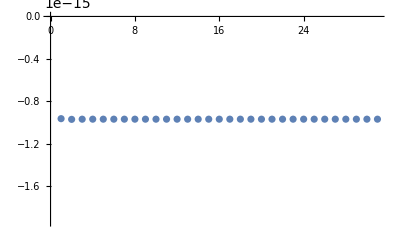

```mathematica
ListPlot[Table[Re[CblockExpansion3[1-0.05,1/2+0.05,n]/.rules],{n,0,30}]]
```

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {1⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification data⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {2⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {3⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification 1.⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {1.⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification 2.⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {2.⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification 3.⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {3.⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

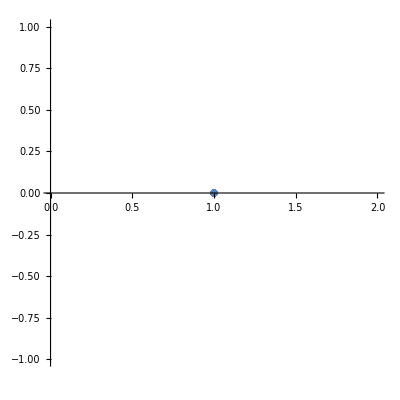

```mathematica
List1 = Table[z/.{z->1},{k,1,20}];
List2=Table[z/.data[[k]][[2]][[2]],{k,1,20}];
ComplexListPlot[{List1,List2}]
```